```mathematica
SetDirectory[NotebookDirectory[]];
(*Makes the notebook’s own folder the current working directory, so relative file paths (Import,Export,Get,etc.) work automatically.*)
```

```mathematica
(*Creates a random Matrix for plots*)
TestMatrix=RandomReal[{0,1},{11,11}];
```

```mathematica
MatrixPlotM[dataA_,AxesLabels_]:=Module[{n,minmax,cf,ticks,Plot,Legend,colorbarTicks,colorbar},
(*Number of elements-- assumed square data matrix (n x n)*)
n=Length[dataA];

(*Range of values for rescaling the color map*)
minmax={0,Max[dataA]};

(*Choice of colormap. A good practice is to use Colorblind-friendly colormaps for inclusion purposes. DeepSeaColors is perceptually uniform and colorblind-friendly.*)
cf=ColorData["DeepSeaColors"];

(*Horizontal tick labels (bottom axis).Labels are centered around zero->i-(n+1)/2. Styled large for readability. You can customize it! *)
ticksH=Table[{i,Style[i-(n+1)/2,40,FontFamily->"Arial"],{0,0}},{i,1,n}]; 

(*Vertical tick labels (left axis).Same as horizontal,but flipped sign so origin is centered. You can customize it!*)
ticksV=Table[{i,Style[-(i-(n+1)/2),40,FontFamily->"Arial"],{0,0}},{i,1,n}];

(*Main matrix plot.
-Reverse+Transpose used to make the origin appear bottom left.
-ColorFunction rescales values into the colormap domain.
-FrameTicks places custom labels only on left and bottom.
-Mesh adds a grid overlay for better cell visibility.*)
Plot=MatrixPlot[Reverse[Transpose[dataA]],
				PlotRange->All,
				ColorFunctionScaling->False,
				ColorFunction->(cf[Rescale[#,minmax]]&),
				Frame->True,
				FrameStyle->White(*Color the mesh*),
				FrameTicks->{{ticksV,None},(*left labels only*){ticksH,None}(*bottom labels only*)},
				FrameLabel->{Style[AxesLabels[[1]],Black,45,FontFamily->"Arial"],(*bottom*)Style[AxesLabels[[2]],Black,45,FontFamily->"Arial"]    (*left*)},
				FrameTicksStyle->Black,
				Axes->False,
				PlotLegends->None,
				ImagePadding->Automatic,
				Mesh->True,              (* Activates the mesh for easier visibility*)
				MeshStyle->White,(*Color the mesh*)
				ImageSize->800]; 

(*Generate labeled tick marks for the colorbar legend*)
colorbarTicks=Table[{x,Style[NumberForm[x,{4,2}],12,FontFamily->"Arial"],{0,0}},{x,minmax[[1]],minmax[[2]],(minmax[[2]]-minmax[[1]])/4}];

(*Colorbar legend:
-Uses same colormap
-Large marker for presentation quality
-Placed horizontally*)
colorbar=BarLegend[{"DeepSeaColors",{0,Max[dataA]}} ,
			LabelStyle->{Black,FontFamily->"Arial",45},
			LegendMarkerSize->{750,50},
			LegendLayout->"Row"]; (*You can chosee "column to make it vertical"*)

Return[{Plot,colorbar}] ]
```

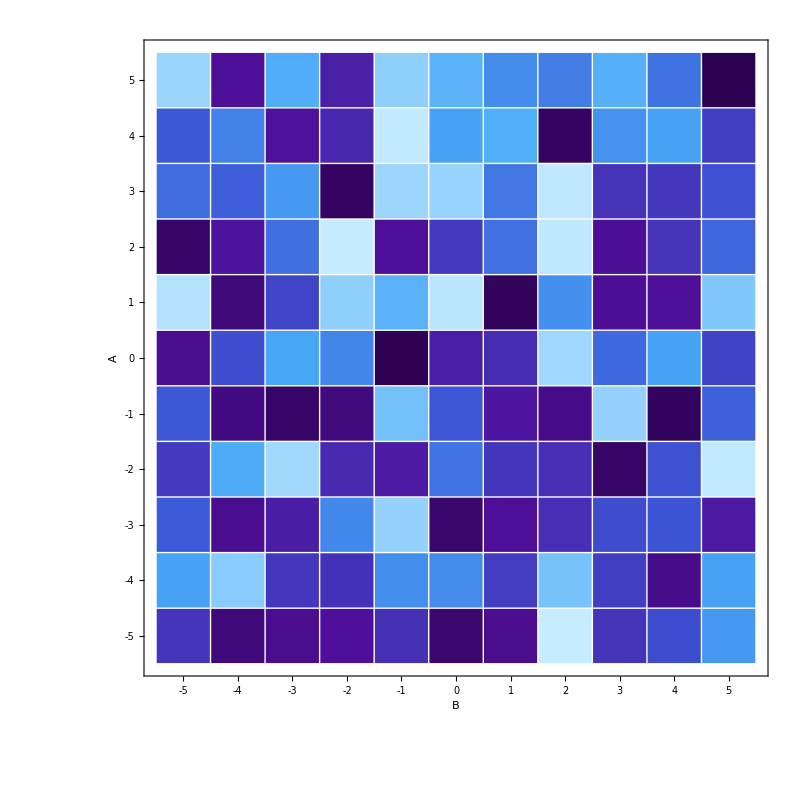

```mathematica
MatrixPlotM[TestMatrix,{"A","B"}]
```